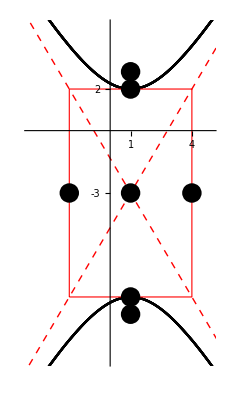

```mathematica
ParametricPlot[
{3Tan[x]+1,5Sec[x]-3},
{x,-20,20},
PlotRange->{{-4,5},{-11,5}},
Ticks->{{1,4},{2,-3}},
PlotStyle->Black,
Epilog->{ 
EdgeForm[{Red, Dashed}],Opacity[0],
Rectangle[{-2,-8},{4,2}],
Opacity[1],Red,Dashed,
InfiniteLine[{{-2,-8},{4,2}}],
InfiniteLine[{{-2,2},{4,-8}}],
PointSize[0.035],Black,Point[{{1,2},{1,-3},{1,-8},{-2,-3},{4,-3},{1,-3+Sqrt[34]},{1,-3-Sqrt[34]}}]
}
]
```